```mathematica
(* Classical Mechanics in Wolfram Language *)
```

```mathematica
(* Kinematics: Projectile motion in 3D with gravity *)
r[t_]:={10t,5 t,20 t-(1/2) 9.8 t^2};
v[t_]:=D[rproj[t],t];
a[t_]:=D[rproj[t],{t,2}];

(* Function *)
r[t]
v[t]
a[t]

(* Trajectory *)
ParametricPlot3D[r[t],{t,0,4},AxesLabel->{"x","y","z"},PlotStyle->Thick]
```

{10 t,5 t,20 t-4.9 t^2}

{10,5,20-9.8 t}

{0,0,-9.8}

-Graphics3D-

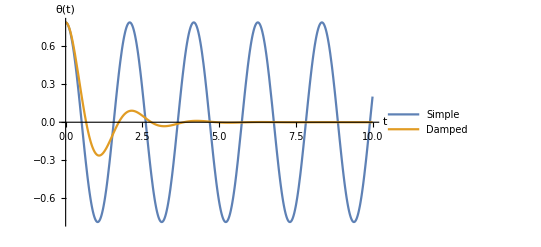

```mathematica
(* Newtonian Mechanics: Pendulum *)
l=1;g=9.8;
theta0=Pi/4;omega0=0;
b=2; (*damping coefficient*)

(* Pendulum without damping *)
solSimple=NDSolve[{theta''[t]+(g/l) Sin[theta[t]]==0,theta[0]==theta0,theta'[0]==omega0},theta,{t,0,10}];

(* Damped Pendulum *)
solDamped=NDSolve[{theta''[t]+b theta'[t]+(g/l) Sin[theta[t]]==0,theta[0]==theta0,theta'[0]==omega0},theta,{t,0,10}];

(* Plot *)
Plot[Evaluate[{theta[t]/. solSimple,theta[t]/. solDamped}],{t,0,10},PlotLegends->{"Simple","Damped"},AxesLabel->{"t","θ(t)"}]

(*Animation*)
Animate[Graphics[{Line[{{0,0},l {Sin[theta[t]/. solDamped[[1]]],-Cos[theta[t]/. solDamped[[1]]]}}],Disk[l {Sin[theta[t]/. solDamped[[1]]],-Cos[theta[t]/. solDamped[[1]]]},0.02]},PlotRange->{{-l,l},{-2 l,0}},Axes->True],{t,0,10}]
```

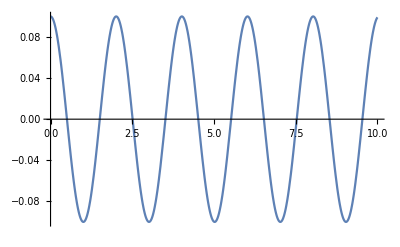

```mathematica
(* Lagrangian Dynamics: Pendulum *)
L=T-V;
T=1/2 m l^2 θ'[t]^2;
V=m g l (1-Cos[θ[t]]);
eq=D[D[L,θ'[t]],t]-D[L,θ[t]]==0;

sol=NDSolve[{eq,θ[0]==0.1,θ'[0]==0},θ,{t,0,10}];
Plot[θ[t]/. sol,{t,0,10}]
```

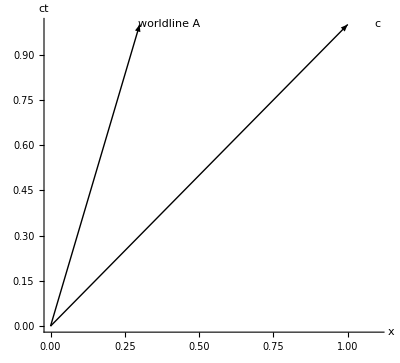

```mathematica
(* Minkowski Diagram & Worldlines *)
Graphics[{Arrow[{{0,0},{1,1}}],Text["c",{1.1,1}],Arrow[{{0,0},{0.3,1}}],Text["worldline A",{0.4,1}]},Axes->True,AxesLabel->{"x","ct"}]
```

```mathematica
(* Gravitational Time Dilation *)
c=1;
Manipulate[Δt Sqrt[1-2 GM/(r c^2)],{{Δt,1},.01,10},{{r,10},.1,100},{{GM,1},.01,10}]
```